Super Mario Bros. is one of the top selling video games of all time. It is known for it's excellently designed platforming levels which has pioneered the platforming video game genre. The project will also use a Convolutional Neural Network which will help determine whether an array is a Mario Level and proceed to generate them using levels from Super Mario Bros. and its sequel Super Mario Bros. The Lost Levels.

## Introduction

Mario is known for it's well crafted level design so attempting to generate them will probably not create the same quality but will hopefully create something similar enough. Super Mario Bros. and Super Mario Bros. The Lost Levels have similar sprites which will help in processing the images.

## Processing Images of Mario Levels

I have collected images of levels from Super Mario Bros. and Super Mario Bros. The Lost Levels. They are all Overworld Levels as their level designs don't differ too much and will have a clearer pattern. I then divide the image into a grid of 16x16px and process each square to map the level into an array.

### Loading the images

I load the images of the levels and crop any extra stuff whilst removing the alpha channel just to simplify it:

```mathematica
map11 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/7c0ee3b5-1a3d-4bd8-a092-7f1f54e4e20d"](https://www.wolframcloud.com/obj/7c0ee3b5-1a3d-4bd8-a092-7f1f54e4e20d)],{{0,0},{-240,0}}]];
map21 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/ac4c0aef-6687-4f31-a240-462039f34d96"](https://www.wolframcloud.com/obj/ac4c0aef-6687-4f31-a240-462039f34d96)],{{0,0},{-240,-240}}]];
map31 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/9bc488a8-13ba-48e6-a60d-3f03f80c9e8b"](https://www.wolframcloud.com/obj/9bc488a8-13ba-48e6-a60d-3f03f80c9e8b)],{{0,0},{-240,-240}}]];
map41 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/6bfbbb3f-cd90-4df1-adc4-4646cc14fb22"](https://www.wolframcloud.com/obj/6bfbbb3f-cd90-4df1-adc4-4646cc14fb22)],{{0,0},{-240,0}}]];
map51 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/17d83563-90ef-4dc9-b97e-51883ffdaccc"](https://www.wolframcloud.com/obj/17d83563-90ef-4dc9-b97e-51883ffdaccc)],{{0,0},{-240,0}}]];
map52 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/916d095e-05ba-4759-a8ae-491755b9f94a"](https://www.wolframcloud.com/obj/916d095e-05ba-4759-a8ae-491755b9f94a)],{{0,0},{-240,-240}}]];
map61 = RemoveAlphaChannel[CloudImport[["https://www.wolframcloud.com/obj/2a8960ac-f087-4151-a73d-28f17ad0f96f"](https://www.wolframcloud.com/obj/2a8960ac-f087-4151-a73d-28f17ad0f96f)]];
map71 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/bb972b44-0a50-480b-90a5-042e4487d72f"](https://www.wolframcloud.com/obj/bb972b44-0a50-480b-90a5-042e4487d72f)],{{0,0},{-240,0}}]];
map81 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/02a7838b-6ac5-4491-a550-6414c3fdd40c"](https://www.wolframcloud.com/obj/02a7838b-6ac5-4491-a550-6414c3fdd40c)],{{0,0},{-240,0}}]];
mapl11 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/65664715-e560-432d-918c-b7be4509ecb0"](https://www.wolframcloud.com/obj/65664715-e560-432d-918c-b7be4509ecb0)],{{0,0},{-240,0}}]];
mapl31 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/9efa1c36-2e01-42f1-8537-ba46c5f4f81a"](https://www.wolframcloud.com/obj/9efa1c36-2e01-42f1-8537-ba46c5f4f81a)],{{0,0},{-240,-240}}]];
mapl41 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/a0861449-e825-42bd-a06d-e56cdced80a8"](https://www.wolframcloud.com/obj/a0861449-e825-42bd-a06d-e56cdced80a8)],{{0,0},{-240,-240}}]];
mapl42 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/d4791678-fb0f-493b-8644-65a3daa12c09"](https://www.wolframcloud.com/obj/d4791678-fb0f-493b-8644-65a3daa12c09)],{{0,0},{-240,0}}]];
mapl61 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/353633ec-e377-4e69-9e62-c6706633d7cd"](https://www.wolframcloud.com/obj/353633ec-e377-4e69-9e62-c6706633d7cd)],{{0,0},{-240,0}}]];
mapl71 = RemoveAlphaChannel[ImagePad[CloudImport[["https://www.wolframcloud.com/obj/1993bd2f-d0b9-44ec-83ec-9e538491dc2a"](https://www.wolframcloud.com/obj/1993bd2f-d0b9-44ec-83ec-9e538491dc2a)],{{0,0},{-240,0}}]];
```

### Creating a function to process each block

Processing each block will help simplify the data whilst not losing any information as Super Mario Bros. was made on a gird.

I get the sprite of each type of block by partitioning the image and taking the position of the block:

```mathematica
ground = ImageData[ImagePartition[map11,16][[-1]][[1]]]|ImageData[ImagePartition[mapl11,16][[-1]][[1]]];
passthrough = ImageData[ImagePartition[map31,16][[-6]][[85]]];
hard =  ImageData[ImagePartition[map11,16][[-3]][[199]]];
lucky =  ImageData[ImagePartition[map11,16][[-6]][[17]]]|ImageData[ImagePartition[map31,16][[-6]][[17]]];
brick =  ImageData[ImagePartition[map11,16][[-6]][[21]]]|ImageData[ImagePartition[mapl11,16][[6]][[20]]];
tpipe =  ImageData[ImagePartition[map11,16][[-6]][[47]]] | ImageData[ImagePartition[map11,16][[-6]][[48]]] | ImageData[ImagePartition[map51,16]⟦-5⟧[[46]]] | ImageData[ImagePartition[map51,16]⟦-5⟧[[45]]]|ImageData[ImagePartition[map31,16][[-4]][[69]]] |ImageData[ImagePartition[map31,16][[-4]][[68]]];
pipe =  ImageData[ImagePartition[map11,16][[-5]][[47]]] | ImageData[ImagePartition[map11,16][[-5]][[48]]] | ImageData[ImagePartition[map51,16]⟦-4⟧[[46]]] | ImageData[ImagePartition[map51,16]⟦-4⟧[[45]]]|ImageData[ImagePartition[map31,16][[-3]][[69]]]|ImageData[ImagePartition[map31,16][[-3]][[68]]];
bullet = ImageData[ImagePartition[map71,16][[-3]][[20]]]|ImageData[ImagePartition[map71,16][[-3]][[29]]]|ImageData[ImagePartition[map71,16][[-3]][[47]]];
```

I then use these values to create a function to transfer each block in the image to a number:

```mathematica
ConvertBlocks[image_]:=Switch[ImageData[image],
ground,1,
hard,1,
lucky,1,
brick,1,
pipe|tpipe,1,
bullet,1,
passthrough,1,
Except["else"],0]
```

I can now convert all of these images into arrays and check the function working through creating an ArrayPlot:

```mathematica
array11=Map[ConvertBlocks,ImagePartition[map11,16],{2}];
array21=Map[ConvertBlocks,ImagePartition[map21,16],{2}];
array31=Map[ConvertBlocks,ImagePartition[map31,16],{2}] ;
array41=Map[ConvertBlocks,ImagePartition[map41,16],{2}];
array51=Map[ConvertBlocks,ImagePartition[map51,16],{2}];
array61=Map[ConvertBlocks,ImagePartition[map61,16],{2}];
array71=Map[ConvertBlocks,ImagePartition[map71,16],{2}];
array81=Map[ConvertBlocks,ImagePartition[map81,16],{2}];
arrayl11 = Map[ConvertBlocks, ImagePartition[mapl11,16],{2}];
arrayl31 = Map[ConvertBlocks, ImagePartition[mapl31,16],{2}];
arrayl41 = Map[ConvertBlocks, ImagePartition[mapl41,16],{2}];
arrayl42 = Map[ConvertBlocks, ImagePartition[mapl42,16],{2}];
arrayl61 = Map[ConvertBlocks, ImagePartition[mapl61,16],{2}];
arrayl71 = Map[ConvertBlocks, ImagePartition[mapl71,16],{2}];
ArrayPlot/@{array11,array21,array31,array41,array51,array61,array71,array81,arrayl11,arrayl31,arrayl41,arrayl42,arrayl61,arrayl71}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Simplifying and Gathering the images

Turning the images into a 15x15 array will give me more data to use and also simplify the whole process as it wouldn't need to generate whole levels but instead sections.

I then create every a 240x240px possible square of each level that doesn't intersect the grid boxes of the level and convert each of those squares into a 15x15 array:

```mathematica
maps = {map11, map21, map31, map41, map51, map52, map61, map71, map81, mapl11, mapl31, mapl41, mapl42, mapl61, mapl71};
imagedataset = Flatten[
      Table[
        Table[ImageTake[map, 240, {i, i + 240 - 1}],
          {i, 1, ImageDimensions[map][[1]] - 240 + 16, 16} (* thx isabel*)
          ], {map, maps}
        ]
      ];
dataset = Map[ConvertBlocks, ImagePartition[#, 16], {2}] & /@ imagedataset;
```

This gives us 3747 squares as shown from the output below:

```mathematica
Dimensions[dataset]
```

{3747,15,15}

## Attempting to generate using a single Wolfram Function

I first attempted trying to generate levels using SequencePredict and LearnDistribution to create Mario Levels which gave an ok output but now a very good one. SequencePredict will take each row whilst LearnDistribution will take in the whole array.

### Using Sequence Predict

I trained SequencePredict on each row of a square to see what it would generate:

```mathematica
sp1 = SequencePredict[Table[entry[[1]],{entry,dataset}]];
sp2 = SequencePredict[Table[entry[[2]],{entry,dataset}]];
sp3 = SequencePredict[Table[entry[[3]],{entry,dataset}]];
sp4 = SequencePredict[Table[entry[[4]],{entry,dataset}]];
sp5 = SequencePredict[Table[entry[[5]],{entry,dataset}]];
sp6 = SequencePredict[Table[entry[[6]],{entry,dataset}]];
sp7 = SequencePredict[Table[entry[[7]],{entry,dataset}]];
sp8 = SequencePredict[Table[entry[[8]],{entry,dataset}]];
sp9 = SequencePredict[Table[entry[[9]],{entry,dataset}]];
sp10 = SequencePredict[Table[entry[[10]],{entry,dataset}]];
sp11= SequencePredict[Table[entry[[11]],{entry,dataset}]];
sp12 = SequencePredict[Table[entry[[12]],{entry,dataset}]];
sp13 = SequencePredict[Table[entry[[13]],{entry,dataset}]];
sp14 = SequencePredict[Table[entry[[14]],{entry,dataset}]];
sp15 = SequencePredict[Table[entry[[15]],{entry,dataset}]];
```

Importing pretrained SequencePredicts:

```mathematica
sp1=CloudGet[["https://www.wolframcloud.com/obj/020de8cf-6a4c-4cc9-bb81-2da5ae83ace2"](https://www.wolframcloud.com/obj/020de8cf-6a4c-4cc9-bb81-2da5ae83ace2)];
sp2=CloudGet[["https://www.wolframcloud.com/obj/cbf306ed-84a5-42fe-9541-dd3fab93339d"](https://www.wolframcloud.com/obj/cbf306ed-84a5-42fe-9541-dd3fab93339d)];
sp3=CloudGet[["https://www.wolframcloud.com/obj/e6a22fb5-5363-4830-a9cc-d13d1d1e201e"](https://www.wolframcloud.com/obj/e6a22fb5-5363-4830-a9cc-d13d1d1e201e)];
sp4=CloudGet[["https://www.wolframcloud.com/obj/c182d57d-7adb-4290-91f9-49fc5aa38690"](https://www.wolframcloud.com/obj/c182d57d-7adb-4290-91f9-49fc5aa38690)];
sp5=CloudGet[["https://www.wolframcloud.com/obj/f9c1f776-2d9c-43ad-b0f2-b8dfd4fcc290"](https://www.wolframcloud.com/obj/f9c1f776-2d9c-43ad-b0f2-b8dfd4fcc290)];
sp6=CloudGet[["https://www.wolframcloud.com/obj/996724cd-d7c2-48fc-b3fe-57e2936ca659"](https://www.wolframcloud.com/obj/996724cd-d7c2-48fc-b3fe-57e2936ca659)];
sp7=CloudGet[["https://www.wolframcloud.com/obj/b06de24f-3494-4821-8d1e-967142e8ddf1"](https://www.wolframcloud.com/obj/b06de24f-3494-4821-8d1e-967142e8ddf1)];
sp8=CloudGet[["https://www.wolframcloud.com/obj/66f4e430-36a0-4f1d-9daa-e6bf572879fe"](https://www.wolframcloud.com/obj/66f4e430-36a0-4f1d-9daa-e6bf572879fe)];
sp9=CloudGet[["https://www.wolframcloud.com/obj/e14a601e-fca4-48ad-8361-965574b07a92"](https://www.wolframcloud.com/obj/e14a601e-fca4-48ad-8361-965574b07a92)];
sp10=CloudGet[["https://www.wolframcloud.com/obj/9e78e55d-c096-4906-bf6c-9c44be13e450"](https://www.wolframcloud.com/obj/9e78e55d-c096-4906-bf6c-9c44be13e450)];
sp11=CloudGet[["https://www.wolframcloud.com/obj/2efe93fd-e375-4e81-8ec3-78b94191eae7"](https://www.wolframcloud.com/obj/2efe93fd-e375-4e81-8ec3-78b94191eae7)];
sp12=CloudGet[["https://www.wolframcloud.com/obj/d4d93ef8-b119-448a-9175-5e4c76fcd6d5"](https://www.wolframcloud.com/obj/d4d93ef8-b119-448a-9175-5e4c76fcd6d5)];
sp13=CloudGet[["https://www.wolframcloud.com/obj/6c9cf4e7-700b-42ce-bec9-b69846d0edf9"](https://www.wolframcloud.com/obj/6c9cf4e7-700b-42ce-bec9-b69846d0edf9)];
sp14=CloudGet[["https://www.wolframcloud.com/obj/daa51e80-10c9-4466-ab66-a26f6b160054"](https://www.wolframcloud.com/obj/daa51e80-10c9-4466-ab66-a26f6b160054)];
sp15=CloudGet[["https://www.wolframcloud.com/obj/9cebeb2a-5f6e-4492-85ce-f05503e34670"](https://www.wolframcloud.com/obj/9cebeb2a-5f6e-4492-85ce-f05503e34670)];
```

I then created an ArrayPlot to visualize how this would look like:

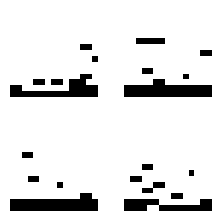

```mathematica
GraphicsGrid[
Table[
Table[
ArrayPlot[{sp1[{0},"RandomNextElement"->15],
sp2[{0},"RandomNextElement"->15],
sp3[{0},"RandomNextElement"->15],
sp4[{0},"RandomNextElement"->15],
sp5[{0},"RandomNextElement"->15],
sp6[{0},"RandomNextElement"->15],
sp7[{0},"RandomNextElement"->15],
sp8[{0},"RandomNextElement"->15],
sp9[{0},"RandomNextElement"->15],
sp10[{0},"RandomNextElement"->15],
sp11[{0},"RandomNextElement"->15],
sp12[{0},"RandomNextElement"->15],
sp13[{0},"RandomNextElement"->15],
sp14[{1},"RandomNextElement"->15],
sp15[{1},"RandomNextElement"->15]}]
,2]
,2]
]
```

### Using Learn Distribution

I then attempted to use Learn Distribution to see what it would produce. I need to change the dataset a bit because Wolfram Language assumes that if there's only 0s then it's a NumericalVector instead of a BooleanVector meaning I'll have decimals so I'll simply change one value to a 1 in the first two rows.

```mathematica
lddataset = dataset;
lddataset[[1]][[1]][[1]] = 1;
lddataset[[1]][[2]][[1]] = 1;
ld = LearnDistribution[lddataset];
```

I then visualized it the same way I did for SequencePredict:

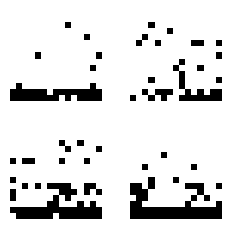

```mathematica
GraphicsGrid[
Table[
Table[
ArrayPlot[RandomVariate[ld]]
,2]
,2]
]
```

Overall the results from SequencePredict look better but LearnDistribution did train faster.

## Attempting to Generate using Learn Distribution

I actually first attempted to generate levels using a GAN but it took too long and the results that came out weren't so good. But the discriminator was working quite well so I decided to replace the generator with LearnDistribution since it trains faster than SequencePredict so I can get results faster. The way I've structured it is that the Discriminator will first be trained on the original Mario Levels and random bad arrays and then LearnDistribution will create their predicted arrays based off learning from the Mario Levels and if the Discriminator thinks what LearnDistribution made was good then it would put it in the arrays for LearnDistribution to learn off from. Whether or not the LearnDistribution's sample was good or not, the discriminator will put it in it's dataset to learn off from as bad.

### The Discriminator

The discriminator is a neural network that determines how close an array is to a Mario Level. The closer the result from putting an array into the discriminator is to 1, the closer the discriminator thinks it's a Mario Level.

It's a simple Convolutional Neural Network:

```mathematica
convolutionBlock[args___]:=NetChain[{ConvolutionLayer[args],NormalizationLayer[],ElementwiseLayer["SELU"],DropoutLayer[0.4]}];
discriminator=NetFlatten@NetChain[{
	convolutionBlock[64,{3,3}],
	convolutionBlock[64,{3,3}],
	LinearLayer[{}],
	LogisticSigmoid
},
	"Input"->{1,15,15}
]
```

NetChain[<>]

We also need to re-format our dataset since the neural network can only take in a 1x15x15 array and not a 15x15:

```mathematica
discriminatorDataset = ArrayReshape[#,{1,15,15}]&/@dataset;
```

We then need to just make a set of bad data as an example:

```mathematica
badDataset=Table[{Table[Table[RandomInteger[],15],15]},1000];
```

Now we need to turn these sets into a set of rules for the neural network to train on:

```mathematica
datasetRules=Join[Table[entry->1,{entry,discriminatorDataset}],Table[entry->0,{entry,badDataset}]];
```

#### The LearnDistribution

LearnDistribution will be used to generate new Mario Levels which, if good, will go back into the LearnDistribution.

We also need to give data to the LearnDistribution so we will first give it the Mario Levels and build on to it:

```mathematica
lddataset = dataset;
lddataset[[1]][[1]][[1]] = 1;
lddataset[[1]][[2]][[1]] = 1;
```

### Putting it all together

We now need to make a few variables to put these all together:

ldlist is every creation from LearnDistribution:

```mathematica
ldlist = {};
```

ldsetrules makes the list of rules to make whatever the LD generates bad:

```mathematica
ldsetrules = {};
```

datagen combines ldsetrules with datasetRules:

```mathematica
datagen = {};
```

goodLD are the samples from LearnDistribution going back to LearnDistribution:

```mathematica
goodLD = {};
```

The variables distrained will now only be used for the trained discriminator and ld will now only be used for the trained LearnDistribution. The following function has three parts, the first is to format the data to put into the discriminator, the second to train the discriminator and LearnDistribution and the third to create new data.

```mathematica
TrainLDNN[rounds_,increase_]:=Table[
ldsetrules=Table[{entry}->0,{entry,ldlist}]; 
datagen = Join[datasetRules,ldsetrules];

distrained = NetTrain[discriminator,datagen,ValidationSet->Scaled[0.2]]; 
ld = LearnDistribution[Join[lddataset,goodLD]];

Table[
randomld = {RandomVariate[ld]};
If[distrained[randomld]>0.999,AppendTo[goodLD,randomld]];
AppendTo[ldlist,randomld];
,increase];
,rounds]
```

The following are pre-trained models for use

```mathematica
distrained=CloudGet[["https://www.wolframcloud.com/obj/1ce759a9-1c08-4b12-9fd3-111c4a6113aa"](https://www.wolframcloud.com/obj/1ce759a9-1c08-4b12-9fd3-111c4a6113aa)];
ld=CloudGet[["https://www.wolframcloud.com/obj/0c38bfe0-7766-4ef0-ac93-75944a87831c"](https://www.wolframcloud.com/obj/0c38bfe0-7766-4ef0-ac93-75944a87831c)];
```

## Finding patterns to make the level more realistic

I'm going to apply general patterns of Mario Levels in order to construct the Mario Level to become more realistic. There are many features in Super Mario Bros such as Bullet Bill Launchers, Pipes, Stairs, Bricks, Lucky Blocks, Clouds and Grass which all have a certain pattern to it. Before using the following functions in this section you have to declare layer1 to 15.

### The First and Second Layers (Very Top Sky)

The first 2 layers are always empty:

```mathematica
layer1 = Table[0,15]
layer2 = Table[0,15]
```

### The Fifteenth and Fourteenth Layers (Ground)

The bottom 2 layers are always identical so whatever the bottom layer is the second bottom layer also is .

The following code will generate the bottom layer and the 2nd bottom layer will just be the same:

```mathematica
layer15 = sp15[{1}, "RandomNextElement" -> 15];
layer14 = layer15
```

{1,1,1,1,1,1,0,0,0,0,0,0,0,1,1}

### The Thirteenth, Twelfth and Eleventh Layer (1 Block above Ground)

For the thirteenth layer the following rules are often applied :

```mathematica
layer13 = sp13[{0},"RandomNextElement"->15]
```

{1,1,1,1,0,1,0,1,1,0,0,0,0,1,1}

If a block is above a gap, remove it:

```mathematica
RemoveFloating[]:=Table[If[layer15[[i]]===0,layer13[[i]]=0,Nothing],{i,15}];
```

```mathematica
RemoveFloating[];
layer13
```

{1,1,1,1,0,1,0,0,0,0,0,0,0,1,1}

If there are just two consecutive blocks with nothing else to the left or right of them then it has to be a pipe:

```mathematica
ReplacePipes[]:=Module[{centerPipeLocations=First[#]+1&/@StringPosition[StringJoin@@ToString/@layer13,"0110"]},
(* For the inside *)
Table[layer13[[index]]=4; layer13[[index+1]] = 5,{index, centerPipeLocations}];
(* For the edges *)
If[layer13[[1]]==1&&layer13[[2]]==1&&layer13[[3]]==0,layer13[[1]]=4;layer13[[2]]=5;,Nothing];
If[layer13[[15]]==1&&layer13[[14]]==1&&layer13[[13]]==0,layer13[[15]]=5;layer13[[14]]=4;,Nothing];
]
```

```mathematica
ReplacePipes[];
layer13
```

{2,2,2,2,0,6,0,0,0,0,0,0,0,4,5}

If there is just one block with nothing else to the left or right of them then it can either be a wall or a bullet bill launcher:

```mathematica
ReplaceLauncher[]:=Module[{centerLauncherLocations=First[#]+1&/@StringPosition[StringJoin@@ToString/@layer13,"010"]},
(* For the inside *)
Table[layer13[[index]]=6,{index,centerLauncherLocations}];
(* For the edges *)
If[layer13[[1]]==1&&layer13[[2]]==0,layer13[[1]]=6;,Nothing];
If[layer13[[15]]==1&&layer13[[14]]==0,layer13[[15]]=6;,Nothing];
]
```

```mathematica
ReplaceLauncher[];
layer13
```

{2,2,2,2,0,6,0,0,0,0,0,0,0,4,5}

If there are more than two consecutive blocks it's most likely a staircase:

```mathematica
ReplaceLayerStairs[]:=Module[{stairsLocations=DeleteDuplicatesBy[StringPosition[StringJoin@@ToString/@layer13,RegularExpression["1{3,}"]],Last]},
Table[layer13[[First[index];;Last[index]]]=2,{index,stairsLocations}];
]
```

```mathematica
ReplaceLayerStairs[];
layer13
```

{2,2,2,2,0,6,0,0,0,0,0,0,0,4,5}

The twelfth an eleventh layer then follow the thirteenth layer with pipes varying from sizes and staircases continuing their pattern.

```mathematica
layer12 = Table[0,15];
layer11 = Table[0,15];
```

To continue from the pipes:

```mathematica
ContinuePipes[]:=Module[{pipeLocations=Position[layer13,4]},
Table[Switch[RandomInteger[2],
2,layer12[[index]]=4;layer12[[index+1]]=5;layer11[[index]]=7;layer11[[index+1]]=8,
1,layer12[[index]]=7; layer12[[index+1]]=8,
0,layer13[[index]]=7; layer13[[index+1]]=8],{index,pipeLocations}];
]
```

```mathematica
ContinuePipes[];
layer11
layer12
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,7,8}

To continue from bullet bills:

```mathematica
ContinueBullet[] := Module[{bulletLocations = Position[layer13, 6]},
  Table[Switch[RandomInteger[2],
     2, layer13[[index]]= "a"; layer12[[index]] = 6; layer11[[index]] = 9,
     1, layer12[[index]] = 9,
     0, layer13[[index]] = 9], {index, bulletLocations}];
  ]
```

```mathematica
ContinueBullet[];
layer11
layer12
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,9,0,0,0,0,0,0,0,7,8}

### Rest of the layers

The rest of the layers either follow a staircase or are bricks and lucky blocks which can be generated from LearnDistribution. Although we did train the LearnDistribution, we will have a certain threshold measured by the LearnDistribution to make sure what it creates is good.

```mathematica
CreateLD:=Module[{quality=0,x=Table[Table[0,15],15]},
While[quality<0.95,
x=RandomVariate[ld];
quality=distrained[{x}];];
x
]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,1,0,1,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1}}

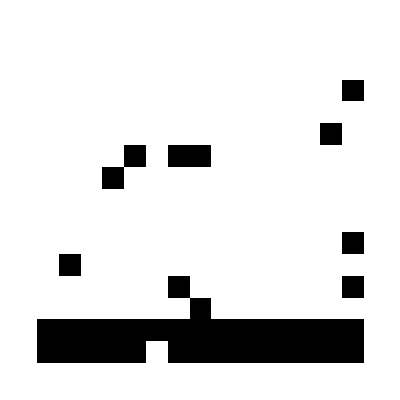

```mathematica
generated =CreateLD
ArrayPlot[generated]
```

I then apply the LearnDistribution to the layers:

```mathematica
layer3 = generated[[3]]/.{1->3};
layer4 = generated[[4]]/.{1->3};
layer5 = generated[[5]]/.{1->3};
layer6 = generated[[6]]/.{1->3};
layer7 = generated[[7]]/.{1->3};
layer8 = generated[[8]]/.{1->3};
layer9 = generated[[9]]/.{1->3};
layer10 = generated[[10]]/.{1->3};
```

### The Stairs

We now need to continue building the stairs which we do after we generate because we want the stairs to have priority.

```mathematica
stairLocs =DeleteDuplicatesBy[StringPosition[StringJoin@@ToString/@layer13,RegularExpression["2{3,}"]],Last];
stairLayers = Reverse[{layer3,layer4,layer5,layer6,layer7,layer8,layer9,layer10,layer11,layer12}];
Table[
Table[
stairLayers[[index]][[First[stairs]+index;;Last[stairs]]]=2,
{index,Min[Last[stairs]-First[stairs],10]}
]
,{stairs,stairLocs}
];
```

```mathematica
layer12=stairLayers[[1]];
layer11=stairLayers[[2]];
layer10=stairLayers[[3]];
layer9=stairLayers[[4]];
layer8=stairLayers[[5]];
layer7=stairLayers[[6]];
layer6=stairLayers[[7]];
layer5=stairLayers[[8]];
layer4=stairLayers[[9]];
layer3=stairLayers[[10]];
```

### The Lucky Blocks

Lucky blocks are often just found on their own.

The following function finds a brick around air and changes it into a lucky block:

```mathematica
ReplaceLucky[layer_]:=Module[{luckylayer=layer,
luckyLocations=First[#]+1&/@StringPosition[StringJoin@@ToString/@layer,"030"]},
Table[luckylayer[[index]]="b",{index,luckyLocations}];
luckylayer
]
```

```mathematica
layer3 = ReplaceLucky[layer3];
layer4 = ReplaceLucky[layer4];
layer5 = ReplaceLucky[layer5];
layer6 = ReplaceLucky[layer6];
layer7 = ReplaceLucky[layer7];
layer8 = ReplaceLucky[layer8];
layer9 = ReplaceLucky[layer9];
layer10 = ReplaceLucky[layer10];
```

### Extra Decorations

Decorations are not interactable but are still important in a Mario level as it helps making the Overworld environment unique.

I then created the following function to add cloud decorations:

```mathematica
ReplaceClouds[]:=Module[{cloudLocs=Map[First,
DeleteCases[
	Gather[
		Join[StringPosition[StringJoin @@ ToString /@ layer3, RegularExpression["0000000"]],StringPosition[StringJoin @@ ToString /@ layer4, RegularExpression["0000000"]]]
	],
{_}]
],
randomCloudLoc={}},

If[Length[cloudLocs]>0,randomCloudLoc=RandomChoice[cloudLocs];
Switch[RandomInteger[2],
0, layer3[[First[randomCloudLoc]]]="c"; layer4[[First[randomCloudLoc]]]="d"; layer3[[First[randomCloudLoc]+1]]="e";  layer4[[First[randomCloudLoc]+1]]="f"; layer3[[First[randomCloudLoc]+2]]="g"; layer4[[First[randomCloudLoc]+2]]="h";,
1,layer3[[First[randomCloudLoc]]]="c"; layer4[[First[randomCloudLoc]]]="d"; Table[layer3[[First[randomCloudLoc]+index]]="e";  layer4[[First[randomCloudLoc]+index]]="f";,{index,2}];layer3[[First[randomCloudLoc]+3]]="g"; layer4[[First[randomCloudLoc]+3]]="h";,
2,layer3[[First[randomCloudLoc]]]="c"; layer4[[First[randomCloudLoc]]]="d"; Table[layer3[[First[randomCloudLoc]+index]]="e";  layer4[[First[randomCloudLoc]+index]]="f";,{index,3}];layer3[[First[randomCloudLoc]+4]]="g"; layer4[[First[randomCloudLoc]+4]]="h";
]
,Nothing];
]
```

I then created the following functions to add grass decorations:

```mathematica
ReplaceBushes[] := Module[{bushLocs = Map[First,
     DeleteCases[
      	Gather[
       		Join[StringPosition[StringJoin @@ ToString /@ layer13, RegularExpression["00000"]], StringPosition[StringJoin @@ ToString /@ layer14, RegularExpression["11111"]]]
       	],
      {_}]
     ],
   randomBushLoc = {}},
  
  If[Length[bushLocs] > 0, randomBushLoc = RandomChoice[bushLocs];
    Switch[RandomInteger[2],
     0, layer13[[First[randomBushLoc]]] = "i"; layer13[[First[randomBushLoc] + 1]] = "j"; layer13[[First[randomBushLoc] + 2]] = "k";,
     1, layer13[[First[randomBushLoc]]] = "i"; Table[layer13[[First[randomBushLoc] + index]] = "j";, {index, 2}]; layer13[[First[randomBushLoc] + 3]] = "k";,
     2, layer13[[First[randomBushLoc]]] = "i"; Table[layer13[[First[randomBushLoc] + index]] = "j";, {index, 3}]; layer13[[First[randomBushLoc] + 4]] = "k";
     ]
    , Nothing];
  ]
```

## Turning the array back into an image

I now want to turn the array back into an image so I've created this function which replaces values back to images

I associate the values to a certain image:

```mathematica
skyback = ImagePartition[map11, 16][[1]][[1]]; (*Sky*)
groundback = ImagePartition[map11, 16][[-1]][[1]]; (*Ground*)
blockback = ImagePartition[map11, 16][[-3]][[199]]; (* Hard Block *)
brickback = ImagePartition[map11, 16][[-6]][[21]]; (* Brick *)
lpipeback = ImagePartition[map11, 16][[-5]][[47]]; (* Left Pipe *)
rpipeback = ImagePartition[map11, 16][[-5]][[48]]; (* Right Pipe *)
bulletback = ImagePartition[map71, 16][[-3]][[20]]; (* Bullet Bill *)
tlpipeback = ImagePartition[map11, 16][[-6]][[47]]; (* Top Left Pipe *)
trpipeback = ImagePartition[map11, 16][[-6]][[48]]; (* Top Right Pipe *)
tbulletback = ImagePartition[map71, 16][[-3]][[29]]; (* Bullet Bill Top *)
bbulletback = ImagePartition[map71, 16][[-3]][[47]]; (* Bullet Bill Bottom *)
luckyback = ImagePartition[map11, 16][[-6]][[17]]; (* Lucky Block *)
tlcloud = ImagePartition[map71, 16][[4]][[31]]; (* Top Left Cloud *)
blcloud = ImagePartition[map71, 16][[5]][[31]]; (* Bottom Left Cloud *)
tcloud = ImagePartition[map71, 16][[3]][[29]]; (* Top Cloud *)
bcloud = ImagePartition[map71, 16][[4]][[29]]; (* Bottom Cloud *)
trcloud = ImagePartition[map71, 16][[3]][[30]]; (* Top Right Cloud *)
brcloud = ImagePartition[map71, 16][[4]][[30]]; (* Bottom Right Cloud *)
lbush = ImagePartition[map11, 16][[13]][[12]]; (* Left Bush *)
bush = ImagePartition[map11, 16][[13]][[13]]; (* Bush *)
rbush = ImagePartition[map11, 16][[13]][[16]]; (* Right Bush *)
ConvertBack[layer_]:=layer/.{0 -> skyback (*Sky*),
  1 -> groundback(*Ground*),
  2 -> blockback (* Hard Block *),
  3 -> brickback (* Brick *),
  4 -> lpipeback (* Left Pipe *),
  5 -> rpipeback (* Right Pipe *),
  6 -> bulletback (* Bullet Bill *),
  7 -> tlpipeback (* Top Left Pipe *),
  8 -> trpipeback (* Top Right Pipe *),
  9 -> tbulletback (* Bullet Bill Top *),
  "a" -> bbulletback (* Bullet Bill Bottom *),
  "b" -> luckyback (* Lucky Block *),
  "c" -> tlcloud (* Top Left Cloud *),
  "d" -> blcloud (* Bottom Left Cloud *),
  "e" -> tcloud (* Top Cloud *),
  "f" -> bcloud (* Bottom Cloud *),
  "g" -> trcloud (* Top Right Cloud *),
  "h" -> brcloud (* Bottom Right Cloud *),
  "i" -> lbush (* Left Bush *),
  "j" -> bush (* Bush *),
  "k" -> rbush (* Right Bush *)}
```

```mathematica
ConvertBack[layer_]:=layer/.
```

I then use ImageAssemble to stitch the image back together

```mathematica
layers={layer1,layer2,layer3,layer4,layer5,layer6,layer7,layer8,layer9,layer10,layer11,layer12,layer13,layer14,layer15};
```

```mathematica
ImageAssemble[Table[ConvertBack[layer],{layer,layers}]]
```

-Graphics-

Wahoo!

## Complete Function

You can now use GenerateMarioLevel[]

```mathematica
GenerateMarioLevel[]:=(
layer1 = Table[0,15];
layer2 = Table[0,15];
layer15 = sp15[{1}, "RandomNextElement" -> 15];
layer14 = layer15;
layer13 = sp13[{0},"RandomNextElement"->15];

RemoveFloating[];
ReplacePipes[];
ReplaceLauncher[];
ReplaceLayerStairs[];

layer12 = Table[0,15];
layer11 = Table[0,15];

ContinuePipes[];
ContinueBullet[];

generated=CreateLD;
layer3 = generated[[3]]/.{1->3};
layer4 = generated[[4]]/.{1->3};
layer5 = generated[[5]]/.{1->3};
layer6 = generated[[6]]/.{1->3};
layer7 = generated[[7]]/.{1->3};
layer8 = generated[[8]]/.{1->3};
layer9 = generated[[9]]/.{1->3};
layer10 = generated[[10]]/.{1->3};

stairLocs =DeleteDuplicatesBy[StringPosition[StringJoin@@ToString/@layer13,RegularExpression["2{3,}"]],Last];
stairLayers = Reverse[{layer3,layer4,layer5,layer6,layer7,layer8,layer9,layer10,layer11,layer12}];
Table[
	Table[
		stairLayers[[index]][[First[stairs]+index;;Last[stairs]]]=2,
		{index,Min[Last[stairs]-First[stairs],10]}
	]
	,{stairs,stairLocs}
];
layer12=stairLayers[[1]];
layer11=stairLayers[[2]];
layer10=stairLayers[[3]];
layer9=stairLayers[[4]];
layer8=stairLayers[[5]];
layer7=stairLayers[[6]];
layer6=stairLayers[[7]];
layer5=stairLayers[[8]];
layer4=stairLayers[[9]];
layer3=stairLayers[[10]];

layer3 = ReplaceLucky[layer3];
layer4 = ReplaceLucky[layer4];
layer5 = ReplaceLucky[layer5];
layer6 = ReplaceLucky[layer6];
layer7 = ReplaceLucky[layer7];
layer8 = ReplaceLucky[layer8];
layer9 = ReplaceLucky[layer9];
layer10 = ReplaceLucky[layer10];

ReplaceClouds[];
ReplaceBushes[];

{layer1,layer2,layer3,layer4,layer5,layer6,layer7,layer8,layer9,layer10,layer11,layer12,layer13,layer14,layer15}
)
```

I then generate an image collage of a variety of generated levels:

```mathematica
Image[ImageCollage[Table[ImageAssemble[Table[ConvertBack[layer],{layer,GenerateMarioLevel[]}]] ,25],ImagePadding->2],ImageSize->Large]
```

-Graphics-

Here's the code to produce just one:

```mathematica
ImageAssemble[Table[ConvertBack[layer],{layer,GenerateMarioLevel[]}]]
```

-Graphics-

## Conclusion & Future Work

I found that the overall result of my project was really good! From the discriminator to the generation process, everything went well enough. If I had more time and resources, I would try using a Deep Convolutional GAN just to see how well that would work in comparison. I would also want to try using ROM Hacking to create the level in Super Mario Bros. and use OpenAI Gym Retro to check its playability. I'd also be interested in doing other level styles such as underground, castle or underwater.

## Acknowledgements

Thank you to my mentor Isabel

## Citations

Super Mario Bros. and Super Mario Bros. The Lost Level Images. The Spriters Resource. (n.d.). Retrieved July 18, 2022, from https://www.spriters-resource.com/

DuplicatesList Function Source. Wolfram Staff. Retrieved July 21 2022, from https://resources.wolframcloud.com/FunctionRepository/resources/DuplicatesList